# calcolo zeri-poli - incubatrice

```mathematica
kp:=x
ki:=0.5
kd:=500
a:=0.0012
```

G(s) = K/(s-a)
C(s) = (k_d * s^2 + k_p * s + k_i)/s
L(s) = (K*k_d * s^2 + K*k_p * s + K*k_i)/(s * (s - a)) = (D * s^2 + P * s + I)/(s * (s - a))
W_r(s) = L(s) / (1 + L(s)) = ((D * s^2 + P * s + I) / ((D + 1) * s^2 + (P - a) * s + I)
z0 = (-P + Sqrt[P^2 - 4*D*I]) /  2D
z1 = (-P - Sqrt[P^2 - 4*D*I]) /  2D
p0  = (-(P-a) + Sqrt[(P-a)^2 - 4*(D+1)*I]) /  2(D+1)
p1  = (-(P-a) + Sqrt[(P-a)^2 - 4*(D+1)*I]) /  2(D+1)

```mathematica
z0:=(-kp+Sqrt[kp^2 - 4*kd*ki])/(2*kd)
z1:=(-kp-Sqrt[kp^2 - 4*kd*ki])/(2*kd)
p0:=(-(kp-a)+Sqrt[(kp-a)^2 - 4*(kd+1)*ki])/(2*(kd+1))
p1:=(-(kp-a)-Sqrt[(kp-a)^2 - 4*(kd+1)*ki])/(2*(kd+1))
```

```mathematica
{z0, p0, z1, p1}
```

{(-x+√(-1000.+x^2))/1000,(0.0012+√(-1002.+(-0.0012+x)^2)-x)/1002,(-x-√(-1000.+x^2))/1000,(0.0012-√(-1002.+(-0.0012+x)^2)-x)/1002}

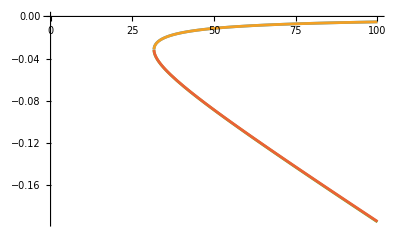

```mathematica
Plot[{z0,p0,z1,p1},{x,0,100}]
```

```mathematica
wn:=Sqrt[ki]
e:=(kp-a)/(2*wn)
mp:=Exp[-Pi*e/Sqrt[1-E^2]]
ts:=3/(e*wn)
tr:=1.8/wn
```

```mathematica
{wn, e, mp, ts, tr}
```

{0.707107,0.707107 (-0.0012+x),ⅇ^((0.+0.878854 ⅈ) (-0.0012+x)),6./(-0.0012+x),2.54558}

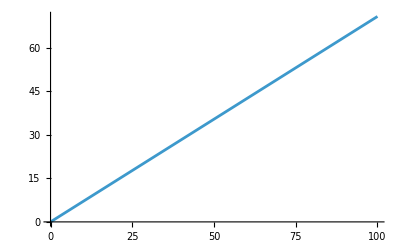

```mathematica
Plot[e,{x,0,100}]
```